Human pose estimation is the task of estimating the positions and orientations of a person’s body joints from images or videos. This project attempts to tackle the 3-dimensional variant of this problem using state-of-the-art computer vision techniques. The CenterNet model is used to obtain 2D keypoints from image frames, estimate the depth of each keypoint using the MiDaS depth estimation model imported via ONNX, and finally scale and visualize the 3D skeletons in an interactive display.

## Introduction

Human pose estimation is a critical computer vision task that involves estimating the positions and orientations of a person’s body joints from an image or a video. It plays a crucial role in a wide range of applications, including action recognition, virtual reality, human-computer interaction, and surveillance systems. The 2D version of pose estimation focuses on inferring joint locations in a 2D image, while the 3D version aims to estimate the 3D positions of the joints, providing a more detailed representation of human movement in physical space. Both variants contribute to understanding human behavior, enabling various practical applications and enhancing our interaction with technology.

This project adopts a two-step approach to estimate 3D human pose. Initially, the 2D coordinates of 17 keypoints on the human body are estimated using CenterNet, a deep learning model designed for object recognition and pose estimation. These 2D coordinates serve as a foundation for understanding joint locations. To extract depth information, we utilize MiDaS, a state-of-the-art monocular depth estimation model. By appending the depths to the 2D coordinates, we establish linkages between body joints and visualize the pose in 3D. The project focuses on single person 3D human pose estimation from images within the Summer School, with preliminary results on single person videos. This integration of 2D and 3D pose estimation techniques contributes to advancing human pose estimation and its practical applications, offering insights into human movement and enabling immersive technologies.
The image below provides a summary of the pipeline for extracting the 3D keypoints.

-Graphics-

## 2D Human Keypoint Estimation

As is the case with most of the state art approaches, the 3D pose estimation problem in this project has been split into two modules. The first module focuses on estimating the 2D keypoints corresponding the joints of humans identified in any image frame. This is done using the CenterNet NetModel.

### CenterNet Pose Estimation Net

CenterNet is a family of models centered around image recognition, object detection and keypoints estimation released in 2019 and incrementally extended since then. The Wolfram Neural Repository contains a NetModel implementation i.e,  CenterNet Pose Estimation Net that has been trained on MS-COCO Data to detect and localize human joints and objects in an image.

```mathematica
centernetModel = NetModel["CenterNet Pose Estimation Nets Trained on MS-COCO Data"]
```

The model takes an image of size 512x512 and gives 8 outputs. Out of these 8, the most relevant to our task is the PoseOffsets, PosePeaks and PoseHeatmaps. The other outputs ports such as ObjectHeatmaps, ObjectPeaks, BoxSizes and BoxOffsets aid in object recognition and mapping in the images.

### Post processing for 2D keypoint extraction

There are 17 heatmaps each corresponding to a joint/keypoint on the human body. Top peaks are extracted by indexing the PosePeaks at high intensity values of the PoseHeatmaps. During the extraction process, peaks below a certain threshold are omitted. The PosePeaks for each joint are then corrected/adjusted using the values from the PoseOffsets array.

#### Keypoint Extraction

```mathematica
labels=;
```

```mathematica
extractTopPeaks[peaks_,heatmap_,topNum_,perChannel_,thresh_:0.1^6]:=Block[{c,h,w,flatHeatmap,flatPeaks,suppresedPeaks,newHeatmap,flatPositions,matrixPositions,topK,channelInd,scores},{c,h,w}=Dimensions[peaks];{flatPeaks,flatHeatmap}=(Transpose[Flatten[Transpose[#1,{3,1,2}],{1,2}]]&)/@{peaks,heatmap};suppresedPeaks=UnitStep[thresh-flatPeaks];newHeatmap=flatHeatmap suppresedPeaks;topK=Min[topNum,w h];flatPositions=(Reverse[Ordering[#1,-topK]]&)/@newHeatmap;matrixPositions=QuotientRemainder[flatPositions-1,w]+1;channelInd=ArrayReshape[Transpose[ConstantArray[Range[c],topK]],{c,topK,1}];matrixPositions=Flatten[Join[channelInd,matrixPositions,3],1];scores=ArrayReshape[Extract[heatmap,matrixPositions],{c,topK}];If[perChannel,Return[{scores,ArrayReshape[matrixPositions-1,{c,topK,3}]}]];flatPositions=Reverse[Ordering[Flatten[scores],-topK]];matrixPositions=matrixPositions⟦flatPositions⟧;scores=Extract[scores,QuotientRemainder[flatPositions-1,topK]+1];{scores,matrixPositions-1}];
filterLowScored[arr_,arrScores_,thresh_]:=Pick[#,UnitStep[arrScores-thresh],1]&/@{arr,arrScores};
Options[decode]={MaxFeatures->100,AcceptanceThreshold->0.1^6,"ObjectDetectionThreshold"->0.5,"HumanPoseThreshold"->0.4,TargetDevice->"CPU"};
decode[net_,img_Image,opts:OptionsPattern[]]:=Block[
{w,h,fh,fw,numKeypoints,postprocessF,scale,netOut,objectScores,objectPeaks,shiftedObjectCenters,hw,boxes,detectedClasses,personPeaks,personScores,numPeople,selectedPoseSizes,regressedPosesAtCenters,poseScores,posePeaks,poseOffsets,candidatePoses,candidatePoseScores},{w,h}=ImageDimensions[img];netOut=net[img,TargetDevice->OptionValue[TargetDevice]];{numKeypoints,fh,fw}=Dimensions[netOut["PoseHeatmaps"]];scale=Max[N[{w,h}/{fw,fh}]];postprocessF[{y_,x_}]:={x scale,h-y scale};{objectScores,objectPeaks}=extractTopPeaks[netOut["ObjectPeaks"],netOut["ObjectHeatmaps"],OptionValue[MaxFeatures],False,OptionValue[AcceptanceThreshold]];{objectPeaks,objectScores}=filterLowScored[objectPeaks,objectScores,OptionValue["ObjectDetectionThreshold"]];If[Length[objectPeaks]==0,Return[{}]];shiftedObjectCenters=objectPeaks⟦All,2;;All⟧+Extract[netOut["BoxOffsets"],Prepend[All]/@(objectPeaks⟦All,2;;All⟧+1)];hw=Extract[netOut["BoxSizes"],Prepend[All]/@(objectPeaks⟦All,2;;All⟧+1)];boxes=Transpose[{shiftedObjectCenters-0.5 hw,shiftedObjectCenters+0.5 hw}];boxes=Rectangle@@@Map[postprocessF,boxes,{2}];detectedClasses=labels⟦objectPeaks⟦All,1⟧+1⟧;{personPeaks,personScores}=(Pick[#1,UnitStep[-objectPeaks⟦All,1⟧],1]&)/@{objectPeaks⟦All,2;;All⟧,objectScores};numPeople=Length[personPeaks];If[numPeople==0,Return[Association["Object Detection"->Transpose[{boxes,detectedClasses,objectScores}]]]];selectedPoseSizes=Transpose[ArrayReshape[Extract[netOut["PoseSizes"],Prepend[All]/@(personPeaks+1)],{numPeople,numKeypoints,2}]];regressedPosesAtCenters=ConstantArray[personPeaks,numKeypoints]+selectedPoseSizes;{poseScores,posePeaks}=extractTopPeaks[netOut["PosePeaks"],netOut["PoseHeatmaps"],OptionValue[MaxFeatures],True,OptionValue[AcceptanceThreshold]];poseOffsets=Extract[Transpose[ArrayReshape[netOut["PoseOffsets"],{numKeypoints,2,fh,fw}]],Prepend[All]/@(Flatten[posePeaks,1]+1)];candidatePoses=ArrayReshape[poseOffsets,{numKeypoints,Length[poseOffsets]/numKeypoints,2}]+posePeaks⟦All,All,2;;All⟧;{candidatePoses,candidatePoseScores}=filterLowScored[candidatePoses,poseScores,OptionValue["HumanPoseThreshold"]];{candidatePoses,regressedPosesAtCenters}=(Map[postprocessF,#1,{2}]&)/@{candidatePoses,regressedPosesAtCenters};Association["Candidate Keypoints"->{candidatePoses,candidatePoseScores},"Keypoints Regressed At Object Centers"->{regressedPosesAtCenters,personScores},"ObjectDetection"->Transpose[{boxes,detectedClasses,objectScores}]]
];
```

As a part of post processing, an alignment operation is done where the person dependent keypoints are best matched to person agnostic accurate keypoint values. Points which are occluded and are unidentifiable are replaced with the missing values.

#### Keypoint Alignment

```mathematica
Options[alignKeypoints]={"NeighborhoodRadius"->Infinity,"FilterOutsideDetections"->True};
alignKeypoints[predictions_Association,opts:OptionsPattern[]]:=Block[
{smartExtract,alignedIds,detections,alignedKeypoints,alignedScores,result,nearestF,insideBoundingBoxQ},
If[Length[predictions]<1,Return[predictions]];
result=KeyTake[predictions,"ObjectDetection"];
If[Length[predictions]==1,Return[result]];
nearestF=If[MatchQ[#,{}],
Function[{inp},{{}}],
Nearest[#->"Index"]
]&/@First[predictions["Candidate Keypoints"]];
alignedIds=MapThread[#1[#2,{1,OptionValue["NeighborhoodRadius"]}]&,
{nearestF,First[predictions["Keypoints Regressed At Object Centers"]]}
];
smartExtract[expr_,positions_]:=Extract[expr,#]&/@positions;
{alignedKeypoints,alignedScores}=Transpose@MapThread[
smartExtract,{#,alignedIds}
]&/@predictions["Candidate Keypoints"];
detections=Select[predictions["ObjectDetection"],#[[2]]=="person"&][[All,1]];
(*Filter the keypoints outside of the bounding boxes*)
If[OptionValue["FilterOutsideDetections"],
insideBoundingBoxQ=MapThread[#1[#2]&,
{RegionMember/@detections,alignedKeypoints/.{}->{$MaxMachineNumber,$MaxMachineNumber}}
];
{alignedKeypoints,alignedScores}=ReplaceAt[#,_->{},Position[insideBoundingBoxQ,False]]&/@{alignedKeypoints,alignedScores}
];
{alignedKeypoints,alignedScores}={alignedKeypoints,alignedScores}/.{}->Missing[];
result["KeypointEstimation"]=alignedKeypoints;
result["KeypointConfidence"]=alignedScores;
result
]
```

A top level function netevaluate takes in the image and returns predictions for object detection, keypoint estimation and keypoint confidence.

```mathematica
Options[netevaluate]=Join[Options[alignKeypoints],Options[decode]];
netevaluate[net_,img_Image,opts:OptionsPattern[]]:=Block[{scale,predictions},predictions=decode[net,img,Sequence@@DeleteCases[{opts},"NeighborhoodRadius"|"FilterOutsideDetections"->_]];
scale=Max@N[ImageDimensions[img]/Reverse@Rest@NetExtract[net,NetPort["PosePeaks"]]];alignKeypoints[predictions,"FilterOutsideDetections"->OptionValue["FilterOutsideDetections"],"NeighborhoodRadius"->OptionValue["NeighborhoodRadius"]*scale]]
```

The following lines of code demonstrate the model in action

```mathematica
testImage = -Graphics-;
```

```mathematica
predictions=netevaluate[centernetModel,testImage];
```

```mathematica
classes=DeleteDuplicates@Flatten@predictions[["ObjectDetection",All,2]]
```

{person}

```mathematica
keypoints=predictions["KeypointEstimation"];
```

```mathematica
HighlightImage[testImage,DeleteMissing[keypoints,2]]//ImageResize[#,{128, Automatic}]&
```

-Graphics-

Using the joint connection information as a list of tuples, we can now plot the skeleton.

```mathematica
jointIndices = ;
getSkeleton[personKeypoints_]:=Line[DeleteMissing[Map[personKeypoints[[#]]&, jointIndices],1,2]]
```

```mathematica
HighlightImage[testImage,Append[AssociationThread[Range[Length[#]]->#]&/@{keypoints,Map[getSkeleton,keypoints]},GroupBy[predictions["ObjectDetection"][[All, ;;2]],Last->First]],ImageLabels->None]
```

-Graphics-

## Depth Estimation of the Keypoints

The next step involves obtaining the depths i.e, z coordinates of the 2D keypoints extracted from the CenterNet. The general idea was to use a monocular depth estimation model to obtain the z value at (x,y) joint location in the image. First attempt was using the Single Image Depth Perceptron Net trained on NYU Depth V2 and Depth in the Wild Data from the Wolfram Neural Network Repository. Due to unsatisfactory results and large inference time, this approach was dropped and alternatively, MiDaS, a monocular depth estimation vision transformer released in 2022, was imported via onnx and used to capture the depths.

### Single Image Depth Perceptron Net

Released in 2016, this neural net was trained to predict the relative depth map from a single image using a novel technique based on sparse ordinal annotations. The model takes in an RGB image of size 3 x 320 x 240 and returns a depth map of size 320 x 240. To make it consistent with the CenterNet framework, the encoder was replaced to accept images of 512 x 512 dimensions

```mathematica
depthNet = NetModel["Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data"]
```

-Graphics-

```mathematica
depthNet=NetReplacePart[depthNet,"Input"->NetEncoder[{"Image",{512, 512}}]]
```

-Graphics-

Testing it on the testImage from the previous section. Some images have an alpha channel in addition to RGB. It is removed before passing to the depthMap.

```mathematica
rescaledTestImage = ImageResize[RemoveAlphaChannel[testImage], {512, 512}];
```

```mathematica
depthMap = depthNet[rescaledTestImage];
```

```mathematica
ListPlot3D[-Reverse@depthMap,PlotStyle->Texture[rescaledTestImage],PlotTheme->{"Minimal","NoAxes"},ViewPoint->{0,-0.96,1.84}]
```

-Graphics-

The average time it takes for the Depth Perceptron net to inference depths from an image on my machine is

```mathematica
Mean@Table[First@Timing[depthNet[rescaledTestImage]],5]
```

0.009375

Plotting a histogram of the image depths reveals their concentration in the range of approximately -10 to 10. The variance, calculated at just 14, significantly constrains the potential for visualizing depth variations.

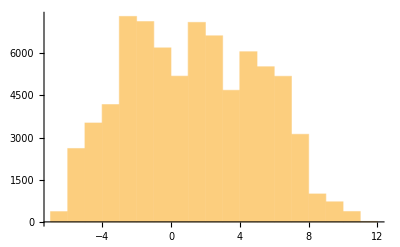

```mathematica
Histogram[depthMap//Flatten]
```

```mathematica
Variance[depthMap//Flatten]
```

14.5655

### MiDaS - Monocular Depth Estimation Net

Implemented using pytorch, MiDaS is a state of art monocular depth estimation model released in 2022 that estimates depth differences in different parts of the foreground objects with good accuracy and more efficiently. The model was exported to ONNX (Open Neural Network Exchange) format using this script provided in the repository.

The model can be downloaded from here. The model can be imported as a NetGraph using the following code by providing the path.

```mathematica
depthMidasNet = Import[FileNameJoin[{NotebookDirectory[],"MiDaS-model-f6b98070.onnx"}]]
```

The model takes in an RGB image of dimensions 3 x 384 x 384 and returns a depth map of size 384 x 384. Let’s scale the image and reorder the channels as needed by the model.

```mathematica
rescaledMidasTestImage = Transpose[ImageData[ImageResize[RemoveAlphaChannel[testImage], {384, 384}]], {2,3,1}];
```

```mathematica
depthMapMidas = depthMidasNet[rescaledMidasTestImage];
```

```mathematica
ListPlot3D[Reverse@depthMapMidas,PlotStyle->Texture[ImageResize[RemoveAlphaChannel[testImage], {384, 384}]],PlotTheme->{"Minimal","NoAxes"},ViewPoint->{0,-0.96,1.84}]
```

The average time it takes for the MiDaS mode to inference depths from an image on my machine is

```mathematica
Mean@Table[First@Timing[depthMidasNet[rescaledMidasTestImage]],5]
```

0.00625

The inference using MiDaS is experimentally 1.5 times faster than on the Depth Perception Net.

The image depth histogram shows concentrations primarily within the 0 to 5000 range. With a variance of around 1700000, even the smallest depth changes can be visualized effectively. This surpasses the previous depth model by offering a wider range and better sensitivity to subtle depth variations.

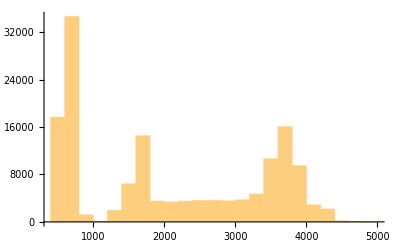

```mathematica
Histogram[depthMapMidas//Flatten]
```

```mathematica
Variance[depthMapMidas//Flatten]
```

1.70358×10^6

## Combining the models together

Now that we have both the 2D keypoints and the depths covered, we can combine the two by modifying the utility function definitions we earlier defined for CenterNet.

The decode function which generates an association has been modified to fetch the depth for every pose peak offset (x,y) from the depth map and append it to the candidate poses as the third coordinate. Fetching depth has been coded in the getDepth function below. In addition, the postprocessF has been modified such that the x and y are now scaled between 0 and 1 instead of in the image coordinates.

```mathematica
getDepth[sublist_,depthmap_]:= Append[#,depthmap[[#[[2]]+1,#[[3]]+1]]]&/@sublist;
Options[decode]={MaxFeatures->100,AcceptanceThreshold->0.1^6,"ObjectDetectionThreshold"->0.5,"HumanPoseThreshold"->0.4,TargetDevice->"CPU"};
decode[net_,img_Image,depthMap_, opts:OptionsPattern[]]:=Block[
{w,h,fh,fw,numKeypoints,postprocessF,scale,netOut,objectScores,objectPeaks,shiftedObjectCenters,hw,boxes,detectedClasses,personPeaks,personScores,numPeople,selectedPoseSizes,regressedPosesAtCenters,poseScores,posePeaks,poseOffsets,candidatePoses,candidatePoseScores, depthPeaks, poseOffsetsNew, regressedPosesAtCentersNew},
{w,h}=ImageDimensions[img];netOut=net[img, TargetDevice->OptionValue[TargetDevice]];{numKeypoints,fh,fw}=Dimensions[netOut["PoseHeatmaps"]];scale=Max[N[{w,h}/{fw,fh}]];
(* Modify the postprocessF method to scale x,y in [0,1[ and take the z coordinate optionally and return its scaled value*)
postprocessF[{y_,x_, z_:Missing[]}]:=If[MissingQ[z],{x/fw,y/fh},{x/fw,y/fh,z}];
{objectScores,objectPeaks}=extractTopPeaks[netOut["ObjectPeaks"],netOut["ObjectHeatmaps"],OptionValue[MaxFeatures],False,OptionValue[AcceptanceThreshold]];{objectPeaks,objectScores}=filterLowScored[objectPeaks,objectScores,OptionValue["ObjectDetectionThreshold"]];If[Length[objectPeaks]==0,Return[{}]];shiftedObjectCenters=objectPeaks⟦All,2;;All⟧+Extract[netOut["BoxOffsets"],Prepend[All]/@(objectPeaks⟦All,2;;All⟧+1)];hw=Extract[netOut["BoxSizes"],Prepend[All]/@(objectPeaks⟦All,2;;All⟧+1)];boxes=Transpose[{shiftedObjectCenters-0.5 hw,shiftedObjectCenters+0.5 hw}];boxes=Rectangle@@@Map[postprocessF,boxes,{2}];detectedClasses=labels⟦objectPeaks⟦All,1⟧+1⟧;{personPeaks,personScores}=(Pick[#1,UnitStep[-objectPeaks⟦All,1⟧],1]&)/@{objectPeaks⟦All,2;;All⟧,objectScores};numPeople=Length[personPeaks];If[numPeople==0,Return[Association["Object Detection"->Transpose[{boxes,detectedClasses,objectScores}]]]];selectedPoseSizes=Transpose[ArrayReshape[Extract[netOut["PoseSizes"],Prepend[All]/@(personPeaks+1)],{numPeople,numKeypoints,2}]];regressedPosesAtCenters=ConstantArray[personPeaks,numKeypoints]+selectedPoseSizes;
{poseScores,posePeaks}=extractTopPeaks[netOut["PosePeaks"],netOut["PoseHeatmaps"],OptionValue[MaxFeatures],True,OptionValue[AcceptanceThreshold]];
(* For every peak (x,y), fetch the depth/z-value from the depth map*)
depthPeaks = Map[getDepth[#,depthMap]&,posePeaks];
poseOffsets=Extract[Transpose[ArrayReshape[netOut["PoseOffsets"],{numKeypoints,2,fh,fw}]],Prepend[All]/@(Flatten[posePeaks,1]+1)];
poseOffsetsNew = Map[Append[#,0]&,poseOffsets];
(* Reshape the 2D pose offsets to 3D and add depthpeaks as the z-coordinate to get candidate poses*)
candidatePoses=ArrayReshape[poseOffsetsNew,{numKeypoints,Length[poseOffsets]/numKeypoints,3}]+depthPeaks[[All,All,2;;All]];
{candidatePoses,candidatePoseScores}=filterLowScored[candidatePoses,poseScores,OptionValue["HumanPoseThreshold"]];
regressedPosesAtCentersNew = Map[Append[#,0]&,regressedPosesAtCenters, {2}];
{candidatePoses,regressedPosesAtCenters}=(Map[postprocessF,#1,{2}]&)/@{candidatePoses,regressedPosesAtCentersNew};Association["Candidate Keypoints"->{candidatePoses,candidatePoseScores},"Keypoints Regressed At Object Centers"->{regressedPosesAtCenters,personScores},"ObjectDetection"->Transpose[{boxes,detectedClasses,objectScores}]]
];
```

The netevaluate function has to be modified so that it takes the MiDaS depth net as an argument, computes the depth map of the image and then pass it to the decode function.

```mathematica
Options[netevaluate]=Join[Options[alignKeypoints],Options[decode]];
netevaluate[net_, depthNet_, img_Image,opts:OptionsPattern[]]:=Block[{scale,predictions, depthMap},
(* Compute the depth map of the image using the depth network *)
depthMap =ImageData[ImageResize[ Image[depthNet[Transpose[ImageData[ImageResize[RemoveAlphaChannel[img], {384,384}]],{2,3,1}]]], {512,512}]];
predictions=decode[net,img,depthMap, Sequence@@DeleteCases[{opts},"NeighborhoodRadius"|"FilterOutsideDetections"->_]];
scale=Max@N[ImageDimensions[img]/Reverse@Rest@NetExtract[net,NetPort["PosePeaks"]]];
alignKeypoints[predictions,"FilterOutsideDetections"->False,"NeighborhoodRadius"->OptionValue["NeighborhoodRadius"]*scale]]
```

Now let’s head to the next section to see the results!

## Visualization and Results

Let’s start with this test image.

```mathematica
testImage = -Graphics-;
```

We get the following output from the netevaluate function called on the testImage.

```mathematica
predictions=netevaluate[centernetModel,depthMidasNet, testImage];
Keys[predictions]
```

{ObjectDetection,KeypointEstimation,KeypointConfidence}

Looking at the keypoints, we can now observe that they are 3-dimensional,

```mathematica
keypoints=predictions["KeypointEstimation"]
```

```mathematica
Dimensions[keypoints[[1,1]]]
```

{3}

For the ease of processing the visualization, we replace the Missing[] keypoints by a vector of 3 Missing[] coordinate values i.e, {Missing[], Missing[], Missing[]}.

```mathematica
keypoints = keypoints/.Missing[]->{Missing[], Missing[], Missing[]}
```

Next, we scale the z values obtained from the depth model ranging from 0 to any positive number to between 0.4 to 0.6 inclusive. Since x and y are already scaled from 0 to 1, we must scale z within the same unit square. The center remains at 0.5 to keep the skeleton centered in the visualization. The 0.2 depth range is based on the average human height-to-depth ratio of 1:7. This means the height should theoretically span a range of 0.14. However, accounting for the possibility of outstretched arms or legs, we round this up to 0.2.

```mathematica
minZ=Min[Map[If[MissingQ[#[[3]]],Nothing,#[[3]]]& ,Flatten[keypoints,1]]];
maxZ=Max[Map[If[MissingQ[#[[3]]],Nothing,#[[3]]]& ,Flatten[keypoints,1]]];
```

```mathematica
keypoints= (MapAt[If[MissingQ[#],Missing[],((#-minZ)/(maxZ-minZ))*(0.2)+0.4]&,keypoints,{All,All,3}])
```

We can try plotting the points in a 3D plot to see the preliminary results.

```mathematica
ListPointPlot3D[DeleteMissing[keypoints,2, 1],PlotStyle->PointSize[0.02], AxesLabel->{x,y,z}, Axes->True]
```

-Graphics-

This view isn’t very helpful. For a decent visualization, joints can be plotted as spheres in 3D and the bones/edges can be plotted as cylinders. The two utility functions defined below take the keypoints and return the corresponding Graphics3D objects.

```mathematica
getJoints[personKeypoints_]:=Map[If[Not@MissingQ[#[[1]]],{RGBColor[0.93, 0.9500000000000001, 0.9686274509803922], Sphere[{#},Scaled[0.007]]},Nothing]&, personKeypoints]
```

```mathematica
getBones[personKeypoints_]:=
Map[If[Not@MissingQ[personKeypoints[[#[[1]]]][[1]]] && Not@MissingQ[personKeypoints[[#[[2]]]][[1]]], {Thickness[0.013], #[[3]], Cylinder[{personKeypoints[[#[[1]]]], personKeypoints[[#[[2]]]]}, 0.007 ]}, Nothing]&,{{1,2,RGBColor[0.9333333333333333, 0.596078431372549, 0.788235294117647]},{1,3, RGBColor[0.6039215686274509, 0.8392156862745098, 0.8392156862745098]},{2,4, RGBColor[0.8862745098039215, 0.4, 0.6745098039215687]},{3,5, RGBColor[0.4627450980392157, 0.7372549019607844, 0.7333333333333333]},{1,6, RGBColor[0.9647058823529412, 0.8, 0.8980392156862745]},{1,7, RGBColor[0.807843137254902, 0.9215686274509803, 0.9254901960784314]},{6,8, RGBColor[0.59, 0.9686274509803922, 0.29]},{8,10,RGBColor[0.48627450980392156, 0.93, 0.33725490196078434]},{7,9,RGBColor[1., 0.403921568627451, 0.4]},{9,11, RGBColor[1., 0.2, 0.20392156862745098]},{6,7, RGBColor[0.9764705882352941, 0.9450980392156862, 0.5490196078431373]},{6,12,RGBColor[1., 0.7176470588235294, 0.5294117647058824] },{7,13, RGBColor[1., 0.5568627450980392, 0.4392156862745098]},{12,13,RGBColor[0.8200000000000001, 0.8666666666666667, 0.5372549019607843]},{12,14, RGBColor[0.8941176470588236, 0.4549019607843137, 0.9686274509803922]},{14,16, RGBColor[0.9098039215686274, 0.30196078431372547, 0.9372549019607843] },{13,15, RGBColor[0.6235294117647059, 0.803921568627451, 0.9686274509803922]},{15,17, RGBColor[0.3058823529411765, 0.6039215686274509, 0.9647058823529412]}}]
```

Combining all of these utilities into a single function to plot the skeleton.

```mathematica
plotSkeletons3D[keypoints_]:= Module[{skeletonBones, skeletonJoints}, 
skeletonBones = Map[getBones,keypoints];
skeletonJoints =Map[getJoints,  keypoints];
Graphics3D[{EdgeForm[None],skeletonBones,skeletonJoints}, Boxed->True,  AxesLabel->{x,y,z},Axes->True, Lighting->{{"Ambient", White}}, ViewVertical->{0, -1, 0}]]
```

We get the following visualization using the plotSkeletons3D function.

```mathematica
skeletonGraphics = plotSkeletons3D[keypoints]
```

-Graphics-

Another meaningful visualization is to have skeleton stand in front of the image for better comparison. The following compact function implements a mesh passing through the two bottom most keypoints and the image overlay in the xy plane given the keypoints.

```mathematica
plotSkeletonsImageOverlay[testImage_, centernetModel_, depthModel_]:= Module[{predictions,keypoints, minZ, maxZ, skeletonBones, skeletonJoints, tileSize, groundPoints, yMin, yMax, mesh, plane, skeletonGraphics}, 
predictions = netevaluate[centernetModel,depthModel, testImage];
keypoints=predictions["KeypointEstimation"]/.Missing[]->{Missing[], Missing[], Missing[]};
minZ=Min[Map[If[MissingQ[#[[3]]],Nothing,#[[3]]]& ,Flatten[keypoints,1]]];
maxZ=Max[Map[If[MissingQ[#[[3]]],Nothing,#[[3]]]& ,Flatten[keypoints,1]]];
keypoints= MapAt[If[MissingQ[#],Missing[],((#-minZ)/(maxZ-minZ))*(0.2)+0.4]&,keypoints,{All,All,3}];
skeletonGraphics = plotSkeletons3D[keypoints];
tileSize=0.2;
groundPoints = TakeLargestBy[DeleteMissing[Flatten[keypoints,1]],#[[2]]&,2];
yMin=groundPoints[[2]][[2]] + 0.2;
yMax=groundPoints[[1]][[2]];mesh=Table[{RGBColor[0.4627450980392157, 0.48, 0.7333333333333333],Cuboid[{i,yMin,j},{i+tileSize,yMax,j+tileSize}]},{i,0,1-tileSize,tileSize},{j,0,1-tileSize,tileSize }];
plane=Polygon[{{0,0,0},{1,0,0},{1,yMin,0},{0,yMax,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}];Show[Graphics3D[mesh],skeletonGraphics, Graphics3D[{Texture[ImageReflect[testImage]],plane},Lighting->{{"Ambient",White}},Boxed->False], ViewProjection->"Orthographic", ViewVertical->{0,-1,0}, Axes->False, Boxed->False]
]
```

```mathematica
plotSkeletonsImageOverlay[testImage, centernetModel, depthMidasNet]
```

-Graphics-

## Extension to Videos

The same utility functions could be used to apply pose estimation on videos by applying them on each frame and animating the output. Let’s import a short video.

```mathematica
videoFrames=Import[FileNameJoin[{NotebookDirectory[], "sample video.mp4"}], "ImageList"];
ImageData[videoFrames[[1]]]//Dimensions
```

{360,640,3}

Applying plotSkeletonsImageOverlay to every frame in the first 250 frames of the video.

```mathematica
skeletonGraphicsList = plotSkeletonsImageOverlay[# , centernetModel, depthMidasNet]&/@videoFrames[[1;;20]];
```

You can play the transformed frames as an animation.

```mathematica
skeletonAnimation = ListAnimate[skeletonGraphicsList]
```

-Graphics-

Exporting the resultant video as mp4.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sample video - skeletons.mp4"}], skeletonGraphicsList, "MP4"];
```

## Future Directions

This project can be extended in several directions.

Multi-person support: The centerNet model has the ability to identify 2D keypoints of multiple persons. Beyond WSS, the project can be extended to estimate 3D keypoints from multiple people within the image yet still group and view them as separate human skeletons.

Occlusion handling: The framework does not give good results when the body parts an occluded. A challenging yet useful future direction would be to implement an occlusion resistant model that can estimate keypoint even if they are hidden by obstacles.

Video Support: Potential ways could be explored to optimize and implement the 3D estimation pipeline for videos.

Mesh Regression: With the 3D points obtained, work can potentially be done to lift the 3D pose to a typical human mesh.

## Concluding remarks

Conclusively, this project explored 3D human pose estimation in the wolfram language. To accomplish this, first 2D keypoints were obtained using the CenterNet model from the Wolfram Neural Network Repository. Next, the pretrained MiDaS Monocular Depth Estimation model was exported as an .onnx file and imported as a NetGraph into WL. This was used to obtain the z-coordinate for the 2D keypoints. The 3D keypoints were visualized using an interactive display. This project serves as a baseline on 3D human pose estimation, especially in WL where no such implementation exists. This can be further built to do complex tasks like mesh regression and human reconstruction.

## Keywords

Pose Estimation

Depth Estimation

Computer Vision

Convolutional Neural Networks

3D Visualization

## Acknowledgment

I would like to thank my mentor, Maria Sargsyan, for her unconditional support and guidance. Thank you for brainstorming with me! I also appreciate our TA, Mark Greenberg, for his helpful tips and debugging. Lastly, I am grateful to Stephen Wolfram for suggesting and inspiring this project.

## References

[1] Ranftl, René, Alexey Bochkovskiy, and Vladlen Koltun. “Vision transformers for dense prediction.” Proceedings of the IEEE/CVF international conference on computer vision. 2021.

[2] Zhou, Xingyi, Dequan Wang, and Philipp Krähenbühl. “Objects as points.” arXiv preprint arXiv:1904.07850 (2019).

## CITE THIS NOTEBOOK

3D human pose estimation using machine learning
by Fizza Rubab
Wolfram Community, STAFF PICKS, July 12, 2023
https://community.wolfram.com/groups/-/m/t/2958416